This Sample file refers to Release 5.0 of PPPC 4 DM ID: see www.marcocirelli.net/PPPC4DMID.html for more details

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Fluxes at production, including EW corrections

Fluxes are given as Log_10[(d N)/(d Log_10 x)]  (x = K/m_DM, with K the kinetic energy in GeV)  normalized per single DM annihilation. 
The format is

	dlNdlxIEW[primary -> secondary][mass, lx]

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	secondary = e, p, γ, d, νe, νμ, ντ	
	mass = m_DM in GeV, on the range m_DM= 5 GeV → 100 TeV
	lx = Log[10, x ], on the range x = 10^-9→ 1 except for the channels V→e, V→μ, V→τ for which x = 10^-5→ 1

Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in x are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/dlNdlxEW.m"];
```

```mathematica
dlNdlxIEW["b"->"e"][1000,Log[10,0.1]]
```

-0.173747

## Fluxes at production, without EW corrections

Fluxes are given as Log_10[(d N)/(d Log_10 x)]  (x = K/m_DM, with K the kinetic energy in GeV)  normalized per single DM annihilation. 
The format is

	dlNdlxI[primary -> secondary][mass, lx]

where

	primary = e, μ, τ, q, c, b, t, W, Z, g, γ, h
	secondary = e, p, γ, d, νe, νμ, ντ	
	mass = m_DM/GeV, on the range m_DM= 5 GeV → 100 TeV
	lx = Log[10, x ], on the range x = 10^-9→ 1
	
Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in x are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/dlNdlxPythia.m"];
```

```mathematica
dlNdlxI["b"->"p"][1000,Log[10,0.1]]
```

-0.165377

## Energy loss coefficient function for electrons and positrons

The function provides provides the energy loss coefficient function b[E, x⃗] for electrons and positrons in the galactic halo.
The units of b[E, x⃗] are GeV/sec.

The format is
	btot[E, r, z, ngasnorm, MF]
where
	E = electron or positron energy in GeV
	r and z = position from the galactic center in cylindrical coordinates in kpc
	ngasnorm allows to change the overall normalization of the gas density
	MF = MF1, MF2, MF3

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/btot.m"];
```

```mathematica
(btot[1,8.33,0,1,"MF1"])^-1
```

5.87366×10^14

## Halo functions for electrons and positrons everywhere in the Galaxy

The functions provide the halo functions I[x,E_s r,z] for electrons (and positrons) at any point in the Galaxy.

The format is

	ElectronHaloFunctGalaxyAnnI[halo, propagation, MF][lx, lEs,r,z]		(for annihilations)
		or
	ElectronHaloFunctGalaxyDecI[halo, propagation, MF][lx, lEs,r,z]		(for decays)

where

	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	lx = Log[10,x]  with  x = E/E_s, E the final energy of the electron (or positron), E_s the initial energy of the electron (or positron)
		with range x = ((10^-3 GeV)/(E_s in GeV)) →1 
	lEs = Log[10,E_s] 
		with range E_s = 10^-3→10^5 GeV
	r = radial galatic coordinate in kpc
		with range r = ~0→20 kpc
	z = height galatic coordinate in kpc
		with range r = 0→L kpc
		
NB: the files are very large, they may take several minutes to load.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronHaloFunctGalaxyAnn.m"];
```

```mathematica
ElectronHaloFunctGalaxyAnnI["Iso","MIN","MF1"][Log[10,10^-1],Log[10,1000],8.33,0]
```

0.664667

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronHaloFunctGalaxyDec.m"];
```

```mathematica
ElectronHaloFunctGalaxyDecI["Bur","MAX","MF1"][Log[10,10^-1],Log[10,1000],8.33,0]
```

1.92912

## Halo functions for electrons and positrons at the location of the Earth

The functions provide the halo functions I[x,E_s r_⊙] for electrons (and positrons) at the location of the Earth.

The format is

	ElectronHaloFunctEarthAnnI[halo, propagation, MF][lx, lEs]		(for annihilations)
		or
	ElectronHaloFunctEarthDecI[halo, propagation, MF][lx, lEs]		(for decays)

where

	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	lx = Log[10,x]  with  x = E/E_s, E the final energy of the electron (or positron), E_sthe initial energy of the electron (or positron)
		with range x = ((10^-3 GeV)/(E_s in GeV)) →1
	lEs = Log[10,E_s] 
		with range E_s = 10^-3→10^5 GeV
	r = radial galatic coordinate in kpc
		with range r = ~0→20 kpc
	z = height galatic coordinate in kpc
		with range r = 0→L kpc

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronHaloFunctEarthAnn.m"];
```

```mathematica
ElectronHaloFunctEarthAnnI["Iso","MIN","MF1"][Log[10,10^-1],Log[10,1000]]
```

0.664667

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronHaloFunctEarthDec.m"];
```

```mathematica
ElectronHaloFunctEarthDecI["Bur","MAX","MF3"][Log[10,10^-1],Log[10,1000]]
```

1.74588

## Fluxes of charged cosmic rays at the Earth, after propagation

### Positrons (annihilation and decay)

The functions provide the fluxes of positrons (and electrons) after propagation to the location of the Earth. But no solar modulation is included. 
Fluxes are given as Log_10[(d Φ)/(d Log_10 E)]  with E the energy in GeV. The units of (d Φ)/(d Log_10 E) are particles/(cm^2 sec sr) .

The format is

	ElectronFluxAnn[primary, halo, propagation, MF][mass, σv, lE]		(for annihilations)
		or
	ElectronFluxDec[primary, halo, propagation, MF][mass, Γ, lE]		(for decays)

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	halo = Bur, Iso, NFW, Ein, EiB, Moo
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	mass = m_DM in GeV, on the range 	m_DM= 5 GeV → 100 TeV (for annihilations)
						or
						m_DM= 10 GeV → 200 TeV (for decay)
	lE = Log[10, E in  GeV], on the range E = 0.3 GeV → 10^5GeV
	σv is the DM annihilation cross section in cm^3/sec
	Γ is the DM decay rate in sec^-1
	
Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in lE are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronFluxAnn.m"];
```

```mathematica
ElectronFluxAnn["b","Ein","MED","MF1"][1000,10^-26,Log[10,100]]
```

-10.3266

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ElectronFluxDec.m"];
```

```mathematica
ElectronFluxDec["b","Ein","MED","MF1"][1000,10^-26,Log[10,100]]
```

-7.04999

### Antiprotons (annihilation and decay)

The functions provide the fluxes of anti-protons after propagation to the location of the Earth. But no solar modulation is included. 
Fluxes are given as Log_10[(d Φ)/(d Log_10 K)]  with K the kinetic energy in GeV. The units of (d Φ)/(d Log_10 K) are particles/(m^2 sec sr) .

The format is

	ProtonFluxELDRAnn[primary, halo, propagation][mass, σv, lK]		(for annihilations)
		or
	ProtonFluxELDRDec[primary, halo, propagation][mass, Γ, lK]		(for decays)

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	mass = m_DM in GeV, on the range 	m_DM= 5 GeV → 100 TeV (for annihilations)
						or
						m_DM= 10 GeV → 200 TeV (for decay)
	lK = Log[10, K in  GeV], on the range K = 10^-1GeV → 10^5GeV (except for the channels V→e, V→μ, V→τ and for m_DM> 10 TeV, in which case K = 1 GeV → 10^5 GeV)
	σv is the DM annihilation cross section in cm^3/sec
	Γ is the DM decay rate in sec^-1

Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in lK are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ProtonFluxELDRAnn.m"];
```

```mathematica
ProtonFluxELDRAnn["b","Ein","MED"][1000,10^-26,Log[10,100]]
```

-4.84849

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ProtonFluxDec.m"];
```

```mathematica
ProtonFluxELDRDec["W","NFW","MED"][1000,10^-26,Log[10,10]]
```

-0.718169

### Antideuterons (annihilation and decay)

The functions provide the fluxes of anti-deuterons after propagation to the location of the Earth. But no solar modulation is included. 
Fluxes are given as Log_10[(d Φ)/(d Log_10(K_d/n))]  with K_d/n  the antideuteron kinetic energy per nucleon in GeV. The units of (d Φ)/(d Log_10(K_d/n)) are particles/(m^2 sec sr) .

The format is

	DeuteronFluxAnn[primary, halo, propagation][mass, σv, lKdn]		(for annihilations)
		or
	DeuteronFluxDec[primary, halo, propagation][mass, Γ, lKdn]		(for decays)

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	mass = m_DM in GeV, on the range 	m_DM= 5 GeV → 100 TeV (for annihilations)
						or
						m_DM= 10 GeV → 200 TeV (for decay)
	lKdn = Log[10, K_d/n  in  GeV], on the range K_d/n = 0.05 GeV → 50000 GeV 
			(except for the channels V→e, V→μ, V→τ and for m_DM> 10 TeV, in which case K_d/n = 0.5 GeV → 50000 GeV)
	σv is the DM annihilation cross section in cm^3/sec
	Γ is the DM decay rate in sec^-1

Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in lKdn are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/DeuteronFluxAnn.m"];
```

```mathematica
DeuteronFluxAnn["b","Ein","MED"][1000,10^-26,Log[10,100]]
```

-8.97707

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/DeuteronFluxDec.m"];
```

```mathematica
DeuteronFluxDec["W","NFW","MED"][1000,10^-26,Log[10,10]]
```

-5.04487

## J factors for gamma rays

The functions provide the factor J(θ) for gamma rays in the cases of annihilations and decays.
The functions are given as Log_10[J(lθ)] with lθ the Log_10 of the angle in radians.

The format is

	lJAnn[halo][Log_10 θ]		(for annihilations)
		or
	lJDec[halo][Log_10 θ]		(for decays)

where
	halo = Bur, Iso, NFW, Ein, EiB, Moo.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/JAnn.m"];
```

```mathematica
10^lJAnn["NFW"][Log[10,π/3]]
```

1.91732

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/JDec.m"];
```

```mathematica
10^lJDec["Iso"][Log[10,10 π/180]]
```

6.06387

## Halo functions for Inverse Compton Scattering

The functions provide the Inverse Compton halo functions  I_IC[E_s,E_γ,ℓ,b].
The units of I_IC are GeV.

The format is

		IICAnnI[halo, propagation, MF][lEs, lEγ, ℓ, b]		(for annihilations)
		or
		IICDecI[halo, propagation, MF][lEs, lEγ, ℓ, b]		(for decays)

where

	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	lEs = Log[10,E_s],  E_s the initial energy of the electron (or positron) in GeV
		with range E_s = 1→10^5 GeV
	lEγ = Log[10,E_γ],  E_γ the photon energy in GeV
		with range E_γ = 10^-2→10^5 GeV	
	ℓ  = longitude in radians
	b = latitude in radians

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IICAnn.m"];
```

```mathematica
10^IICAnnI["EiB","MAX","MF1"][Log[10,1000],Log[10,100],π/4,π/4]
```

160.306

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IICDec.m"];
```

```mathematica
10^IICDecI["EiB","MAX","MF1"][Log[10,1000],Log[10,100],π/4,π/4]
```

197.374

## Code bites to compute Fluxes of ICS gamma rays

These pieces of code allow to compute the fluxes of ICS gamma rays in a given observational window for a custom choice of DM mass, annihilation cross section /decay rate, DM galactic profile and propagation parameters.

### Annihilation

Load the IC halo functions, the fluxes at production and define the basic astronomical parameters (not to be changed):

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IICAnn.m"];
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/dlNdlxEW.m"];
rSun=8.33 10^3 3.08568025 10^18;ρSun=.3;
```

Set the following parameters:
	llos, blos: the longitude and latitude identifying the line of sight, in degrees
		(notice that computations might become unstable for b, l < 0.1 degrees) 
	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	mass = m_DM in GeV, on the range m_DM= 5 GeV → 100 TeV
	σv: annihilation cross section in cm^3/s
	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3

```mathematica
llos=10Degree;
blos=10Degree;
primary = "b";
mDM=100;
σv=10^-26;
halo="NFW";
propagation="MED";
MF="MF1";
```

The following cells compute and plot the differential ICS gamma ray spectrum times E_γ^2, i.e. the quantity  E_γ^2 dΦ_ICγ/dE_γ:

```mathematica
Off[Solve::"ifun",Less::"nord",NIntegrate::"ncvb",NIntegrate::"slwcon"];lΦICS[primary,mDM,halo,propagation,MF,σv,llos,blos]=Interpolation[tablΦ=Table[Eγ=10^lEγ;{lEγ,If[Eγ≤mDM,PrintTemporary[10^lEγ," GeV"];Log10[1/Eγ^2 rSun/(4π)1/2(ρSun/mDM)^2 NIntegrate[(σv 1/mDM 10.^dlNdlxIEW[primary->"e"][mDM,Log[10,EnS/mDM]]/(EnS/mDM)/Log[10])10^IICAnnI[halo,propagation,MF][Log[10,EnS],Log[10,Eγ],llos,blos],{EnS,10^-3,mDM}]],-100]},{lEγ,-3,5,0.1}],InterpolationOrder->1];On[Solve::"ifun",Less::"nord",NIntegrate::"ncvb",NIntegrate::"slwcon"];Clear[Eγ]
```

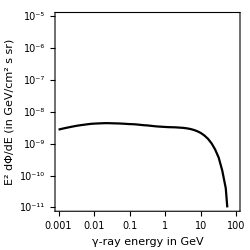

```mathematica
LogLogPlot[Eγ^2 10^(lΦICS[primary,mDM,halo,propagation,MF,σv,llos,blos][Log10[Eγ]]),{Eγ,10^-3,10^2},Frame->True,Axes->False,ImageSize->250,PlotStyle->{Black},AspectRatio->1,PlotRange->{{10^-3,10^2},{10^-11,10^-5}},FrameLabel->{"γ-ray energy in GeV","E^2  dΦ/dE  (in GeV/cm^2 s sr)"}]
```

### Decay

Load the IC halo functions, the fluxes at production and define the basic astronomical parameters (not to be changed):

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IICDec.m"];
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/dlNdlxEW.m"];
rSun=8.33 10^3 3.08568025 10^18;ρSun=.3;
```

Set the following parameters:
	llos, blos: the longitude and latitude identifying the line of sight, in degrees
		(notice that computations might become unstable for b, l < 0.1 degrees) 
	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	mass = m_DM in GeV, on the range m_DM= 5 GeV → 100 TeV
	Γ: decay rate in s^-1
	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3

```mathematica
llos=10Degree;
blos=10Degree;
primary = "b";
mDM=100;
Γ=10^-26;
halo="NFW";
propagation="MED";
MF="MF1";
```

The following cells compute and plot the differential ICS gamma ray spectrum times E_γ^2, i.e. the quantity  E_γ^2 dΦ_ICγ/dE_γ:

```mathematica
Off[Solve::"ifun",Less::"nord",NIntegrate::"ncvb",NIntegrate::"slwcon"];lΦICS[primary,mDM,halo,propagation,MF,Γ,llos,blos]=Interpolation[tablΦ=Table[Eγ=10^lEγ;{lEγ,If[Eγ≤mDM/2,PrintTemporary[10^lEγ," GeV"];Log10[1/Eγ^2 rSun/(4π)(ρSun/mDM) NIntegrate[(Γ 1/(mDM/2) 10.^dlNdlxIEW[primary->"e"][mDM/2,Log[10,EnS/(mDM/2)]]/(EnS/(mDM/2))/Log[10])10^IICDecI[halo,propagation,MF][Log[10,EnS],Log[10,Eγ],llos,blos],{EnS,10^-3,mDM/2}]],-100]},{lEγ,-3,5,0.1}],InterpolationOrder->1];On[Solve::"ifun",Less::"nord",NIntegrate::"ncvb",NIntegrate::"slwcon"];Clear[Eγ]
```

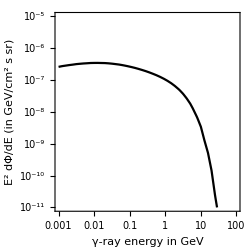

```mathematica
LogLogPlot[Eγ^2 10^(lΦICS[primary,mDM,halo,propagation,MF,Γ,llos,blos][Log10[Eγ]]),{Eγ,10^-3,10^2},Frame->True,Axes->False,ImageSize->250,PlotStyle->{Black},AspectRatio->1,PlotRange->{{10^-3,10^2},{10^-11,10^-5}},FrameLabel->{"γ-ray energy in GeV","E^2  dΦ/dE  (in GeV/cm^2 s sr)"}]
```

## Halo functions for Bremsstrahlung gamma rays

The functions provide the (Log_10 of the) Bremsstrahlung halo functions: Log_10[ I_Brem[E_s,E_γ,ℓ,b] ].
The units of I_Brem are GeV.

The format is

	IBremAnnI[halo, propagation, MF][lEs, lEγ, ℓ, b]		(for annihilations)
		or
	IBremDecI[halo, propagation,MF][lEs, lEγ, ℓ, b]		(for decays)

where

	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	lEs = Log[10,E_s],  E_s the initial energy of the electron (or positron) in GeV
		with range E_s = 1→10^5 GeV
	lEγ = Log[10,E_γ],  E_γ the photon energy in GeV
		with range E_γ = 10^-3→10^5 GeV	
	ℓ = longitude in radians, with range 0 → π, i.e. 0^o→ 180^o
	b = latitude in radians, with range 0 → 0.3490..., i.e. 0^o→ 20^o

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IBremAnn.m"];
```

```mathematica
10^IBremAnnI["EiB","MAX","MF1"][Log[10,1000],Log[10,100],π/4,0]
```

92.3747

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/IBremDec.m"];
```

```mathematica
10^IBremDecI["EiB","MAX","MF1"][Log[10,1000],Log[10,100],π/4,0]
```

55.9381

## Halo functions for Synchrotron radiation

The functions provide the (Log_10 of the) Synchrotron halo functions  Log_10[ I_syn[E_s,ν,ℓ,b] ].
The units of I_syn are erg/Hz.

The format is

	ISynAnnI[halo, propagation, MF][lEs, lν, ℓ, b]		(for annihilations)
		or
	ISynDecI[halo, propagation,MF][lEs, lν, ℓ, b]			(for decays)

where

	halo = Bur, Iso, NFW, Ein, EiB, Moo 
	propagation = MIN, MED, MAX
	MF = MF1, MF2, MF3
	lEs = Log[10,E_s],  E_s the initial energy of the electron (or positron) in GeV
		with range E_s = 10^-3→10^5 GeV
	lν = Log[10,ν],  ν the radio wave frequency in Hz
		with range ν = 10^7→10^11 Hz	
	ℓ = longitude in radians, with range 0 → π, i.e. 0^o→ 180^o
	b = latitude in radians, with range 0 → π/2, i.e. 0^o→ 90^o

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ISynAnn.m"];
```

```mathematica
10^ISynAnnI["Bur","MIN","MF1"][Log[10,1000],Log[10,45 10^6],π/6,0]
```

5.6817×10^9

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/ISynDec.m"];
```

```mathematica
10^ISynDecI["Bur","MIN","MF3"][Log[10,1000],Log[10,45 10^6],π/6,0]
```

7.501×10^9

## Cosmological boost factor

The function provides the cosmological boost factor B(z) as a function of redshift z.

The format is

	BoostF[z, minhalomass, cmodel]
	
where

	minhalomass = 10^-9→ 10^-3(in units of M_⊙)
	cmodel = maccio, powerlaw

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/BoostF.m"];
```

```mathematica
BoostF[6,10^-6,"maccio"]
```

2896.55

## Optical depth of the Universe

The function provides the 'transparency coefficient' for extragalactic gamma rays e^(-τ(E,z')) as a function of the photon energy E and the redshift z'.

The format is

	ETau[E, z', UVmodel]
	
where

	E (= photon energy at detection at Earth) = 2.5 10^-8→ 5 10^5in units of GeV
	z' (= redshift of emission) = 0.01 → 1000
	UVmodel = noUV, minUV, maxUV

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/OpticalDepth.m"];
```

```mathematica
ETau[100,20,"minUV"]
```

0.0309552

## Fluxes of extragalactic gamma rays

The functions provide the fluxes of extragalactic gamma rays.  
Fluxes are given as Log_10[(d Φ)/(d Log_10 E)]  with E the energy in GeV. The units of (d Φ)/(d Log_10 E) are photons/(cm^2 sec sr) .

The format is

	EGgammaFluxAnn[primary, minhalomass, cmodel, UVmodel][mass, σv, lE]		(for annihilations)
		or
	EGgammaFluxDec[primary, UVmodel][mass, Γ, lE]		(for decays)

where

	primary = eL, eR, e, μL, μR, μ, τL, τR, τ, q, c, b, t, WL, WT, W, ZL, ZT, Z, g, γ, h, νe, νμ, ντ, V→e, V→μ, V→τ
	minhalomass = 10^-9 M_⊙, 10^-6 M_⊙
	cmodel = maccio, powerlaw
	UVmodel = noUV, minUV, maxUV
	mass = m_DM in GeV, on the range m_DM= 5 GeV → 100 TeV (for annihilations) 
					      or 
					      m_DM= 10 GeV → 200 TeV (for decay)
	lE = Log[10, E in  GeV], on the range E = 10^-6 m_DM → m_DM
	σv is the DM annihilation cross section in cm^3/sec
	Γ is the DM decay rate in sec^-1
	
Warning:	Extrapolations are performed close to the kinematical threshold for massive primaries (e.g. in the case DM DM -> ZZ with m_DM=93 GeV): the output fluxes should be reliable, but instabilities are possible. Also, instabilities very close to the edges of the domain in lE are possible.

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/EGgammaFluxAnn.m"];
```

```mathematica
EGgammaFluxAnn["b", 10^-6//N,"maccio","minUV"][1000,10^-26,Log[10,100]]
```

-12.4781

```mathematica
Get["/Users/mcirelli/Documents/mathematica/PPPC4DMID/EGgammaFluxDec.m"];
```

```mathematica
EGgammaFluxDec["b","minUV"][1000,10^-26,Log[10,100]]
```

-8.82583

## Neutrinos from the Sun

### DM annihilation rate in the Sun

DM annihilation cross section Γ_ann (= Γ_capt/2) in the center of the Sun.

The format is

	GammaAnn[mass,σ_SI,σ_SD,v_0,v_esc,k]

where 

	mass = M_DM in GeV, on the range 1 GeV→100 TeV
	σ_SI = Spin Independent cross section DM-nucleon, on a single nucleon, in pb
	σ_SD = Spin Dependent cross section DM-nucleon, on a single nucleon, in pb	
	v_0 = velocity parameter in the DM velocity distribution, on the range 220→270 km/s
	v_esc =galactic escape velocity,on the range 450→650 km/s
	k = exponent in the DM velocity distribution, on the range 0→4

```mathematica
Get["GammaAnn.m"];
```

```mathematica
GammaAnn[100000,1,0,250,550,1]
```

2.0104×10^23

### Neutrino energy spectra at production

These are the neutrino fluxes at production in the Sun, including all energy loss effects and EW effects. 

Fluxes are given as Log_10[(d N)/(d Log_10 x)]  (x = E/M_DM, with E the neutrino energy in GeV)  normalized per single DM annihilation. 
The format is

	dlNνdlxIEW[primary -> neutrino][mass,lx]

where 

	primary = b, c, eL, eR, g, h, q, t, WL, WT, ZL, ZT, γ, μL, μR, νe, νμ, ντ, τL, τR
	neutrino = νe, νeb, νμ, νμb, ντ, ντb
	mass =M_DM in GeV,on the rangeM_DM=5 GeV (or the primary mass threshold)→100 TeV
	lx = Log[10,x], on the range x = 10^-9→ 1

```mathematica
Get["dlNnudlxEW.m"];Clear[x,mass]
```

```mathematica
dlNνdlxIEW["b"->"νeb"][100,Log[10,10^-1]]
```

-0.722084

For example, the following is the spectrum of ν_μneutrinos from one annihilation of 1 TeV DM particles into the bb channel:

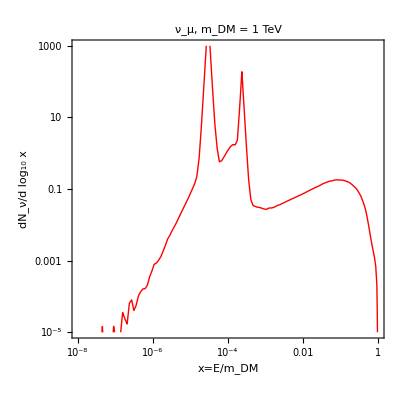

```mathematica
LogLogPlot[10.^dlNνdlxIEW["b"->"νμ"][1000,Log[10,x]],{x,10^-8,1},PlotRange->{10^-5,1000},Frame->True,AspectRatio->1,FrameLabel->{"x=E/m_DM","dN_ν/d log_10 x"},PlotLabel->"ν_μ, m_DM = 1 TeV",PlotStyle->Red]
```

### Neutrino energy spectra at detection

These are the neutrino fluxes at detector’s location, including all propagation effects (in solar matter, oscillations, Earth crossing...). See the paper for all details.  

Fluxes are given as (d N)/(d x)  (x = E/M_DM, with E the neutrino energy in GeV)  normalized per single DM annihilation. 
The format is

	dNνdxEarth[primary -> neutrino, Hierarchy, mass,x, cosθ_zenith]

where 

	primary = b, c, eL, eR, g, h, q, t, WL, WT, ZL, ZT, γ, μL, μR, νe, νμ, ντ, τL, τR
	neutrino = νe, νeb, νμ, νμb, ντ, ντb
	Hierarchy = +1 for Normal, -1 for Inverted
	mass =M_DM in GeV,on the rangeM_DM=5 GeV (or the primary mass threshold)→100 TeV
	x on the range x = 10^-9/mass → 1
	cosθ_zenith= cosine of the zenith angle, on the range -1 → 0 (neutrinos vertically from below: -1, no Earth crossing: 0).

```mathematica
Get["dlNnudlxEarth.m"];Clear[x,prim,fin,Hierarchy,MDM,cθ]
```

```mathematica
dNνdxEarth["b"->"νμ",1,10,10^-2,-1]
```

2.36999

For example, the following is the spectrum of ν_μneutrinos from one annihilation in the Sun of 1 TeV DM particles into the bb channel,  assuming Normal neutrino hierarchy and collected after maximal vertical crossing of the Earth.

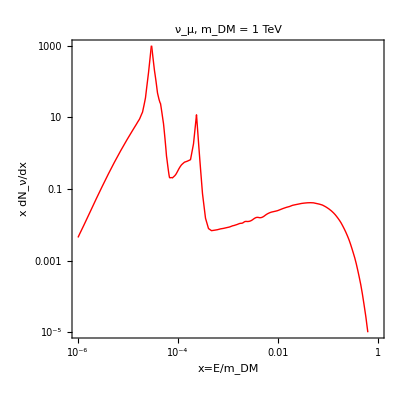

```mathematica
LogLogPlot[x dNνdxEarth["b"->"νμ",1,1000,x,-1],{x,10^-6,1},PlotRange->{10^-5,10^3},Frame->True,AspectRatio->1,FrameLabel->{"x=E/m_DM","x dN_ν/dx"},PlotLabel->"ν_μ, m_DM = 1 TeV",PlotStyle->Red]
```